# Just launch the code below to run the notebook (shift+enter)

```mathematica
ClearAll["Global`*"]
BlockEvaluation[tag_]:=Block[{},
nb=EvaluationNotebook[];
NotebookFind[nb,tag,All,CellTags];
SelectionEvaluate[nb]
]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
infoDialog[phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],Button["Proceed",DialogReturn[choice]]}]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Auxiliary data"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Auxiliary data"}]]];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Auxiliary data/B-3Lmu"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Auxiliary data/B-3Lmu"}]]];
choiceslist={"Acceptance","Tabulated number of events","Sensitivity"};
taglist["Acceptance"]="Acceptance";
taglist["Tabulated number of events"]="Number-of-events";
taglist["Sensitivity"]="Sensitivity";
computationchoice=dropdownDialog[choiceslist,"Do you want to compute the tabulated number of events and then sensitivity, or just sensitivity (if the tabulated number of events has been already produced)?"];
tagselected=taglist[computationchoice]
BlockEvaluation[tagselected]
```

# Definitions

## Parameters

```mathematica
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
infoDialog[phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],Button["Proceed",DialogReturn[choice]]}]]
(*pp cross-section in mb in terms of invariant mass s*)
Z=35.45;
B=0.308;
Y1=42.53;
Y2=33.34;
s0=5.38^2;
s1=1;
η1=0.458;
η2=0.545;
MP=0.938;
S[Pp_,mp_]=2*Pp*mp;
sigmapp[s_]=Z+B*Log[s/s0]^2+Y1*(s1/s)^η1-Y2(s1/s)^η2;
σpNucleonInpb[Atarget_]=51*Atarget^-0.29*10^9;
σppLHC=72*10^9;
(*Invariant mass of two protons in lab frame of one proton*)
SPP[Eplab_]=(Eplab+1)^2-Eplab^2;
S[Pp_,mp_]=2*Pp*mp;
Sprime[mp_,Pp_,PV_]=2*mp*(Pp-PV);
(*Conversion units*)
GeVMinusOneTom=2*10^-16;
chbarval=3*10^8*6.58*10^-25;
(*EM coupling*)
αEM=1/137;
(*Mesons masses*)
mρ0=0.775;
mπ0=0.135;
mη=0.547;
mηpr=0.958;
```

## Phenomenology

## Decays

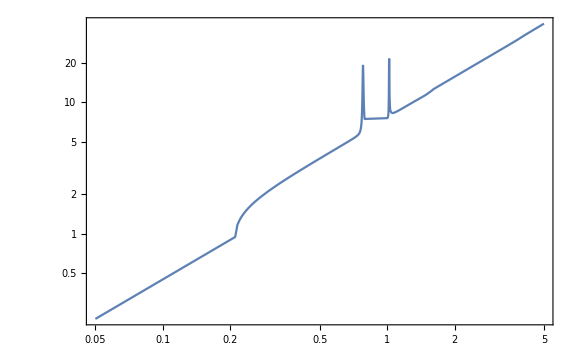

```mathematica
(*Decay width in GeV*)
ΓBL[mV_,αB_]=αB*10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Import[FileNameJoin[{NotebookDirectory[],"phenomenology/B-3Lmu/decay widths/GammaTotBL.txt"}],"Table"],InterpolationOrder->1][Log10[mV]]);
LogLogPlot[ΓBL[mV,1],{mV,0.05,5},Frame->True,ImageSize->Large]
(*Decay length*)
cτBL[mV_,αB_]=chbarval/ΓBL[mV,αB];
ldecayBL[mV_,αB_,EV_]=cτBL[mV,αB]*(√(EV^2-mV^2))/mV;
```

## Production probabilities

### Bremsstrahlung

#### Proton form-factor in timelike region

-(Gω1420 mω1420^2)/(-mω1420^2+q2+ⅈ mω1420 Γω1420)-(Gω1650 mω1650^2)/(-mω1650^2+q2+ⅈ mω1650 Γω1650)-(2.0117 mω780^2)/(-mω780^2+q2+ⅈ mω780 Γω780)

{Gω1420→-2.16606+0.775568 ⅈ,Gω1650→1.15472-0.574419 ⅈ}

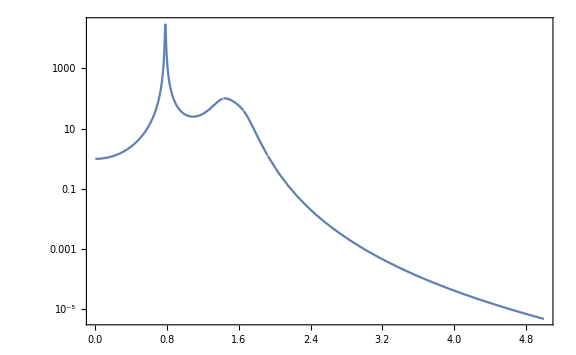

```mathematica
(*The form-factor is derived assuming the mixing of BLs with 3 ρ and 3 ω resonances,with the 6 couplings fixed from experiment (lowest ρ,ω resonances) +boundary conditions)*)
(*Masses and other parameters*)
fωBL=1.011;
fρBL=0.616;
{Mω780,Mω1420,Mω1650}={0.78,1.42,1.65};
{Gammaω780,Gammaω1420,Gammaω1650}={0.0084,0.29,0.315};
Qel=DiagonalMatrix[{2/3,-(1/3),-(1/3)}];
Tω = (1/2)DiagonalMatrix[{1,1,0}];
Tϕ = (1/(√2))DiagonalMatrix[{0,0,1}];
fωN=17.2;
gω=17.1*(((1/3)Tr[Tω])/Tr[Qel.Tω]);
Gω=4(fωN/gω);
FVectorMeson[q2_,mV_,ΓV_]=-(mV^2/(q2-mV^2+I*ΓV*mV));
FormFactorBremBL3ωTemp[q2_,mω780_,mω1420_,mω1650_,Γω780_,Γω1420_,Γω1650_]=Gω*FVectorMeson[q2,mω780,Γω780]+Gω1420*FVectorMeson[q2,mω1420,Γω1420]+Gω1650*FVectorMeson[q2,mω1650,Γω1650]
EquationsBL3ω[mω780_,mω1420_,mω1650_]:={(Limit[FormFactorBremBL3ωTemp[-q2,mω780,mω1420,mω1650,Gammaω780,Gammaω1420,Gammaω1650]q2,q2->Infinity])==0&&FormFactorBremBL3ωTemp[0,mω780,mω1420,mω1650,Gammaω780,Gammaω1420,Gammaω1650]==1}
solFormBL3ω=Solve[EquationsBL3ω[Mω780,Mω1420,Mω1650],{Gω1420,Gω1650}][[1]]
FormFactorBremBL[q_]=Abs[FormFactorBremBL3ωTemp[q^2,Mω780,Mω1420,Mω1650,Gammaω780,Gammaω1420,Gammaω1650]/.{Gω1420->(Gω1420/.solFormBL3ω)}/.{Gω1650->(Gω1650/.solFormBL3ω)}];
LogPlot[FormFactorBremBL[mV]^2,{mV,0.0,5},PlotRange->All,Frame->True,ImageSize->Large]
```

#### Bremsstrahlung probability

```mathematica
(*Double differential cross-section (d^2 Subscript[σ, brem])/(Subscript[dp, T] dz), where Subscript[p, T] is the BL's transverse momentum and z = Subscript[E, BL]/Subscript[p, beam]*)
H1[z_,pT_,mp_,mV_]=pT^2+(1-z)*mV^2+z^2*mp^2;
d2NdpTdz[mp_,z_,pT_,Pp_,mV_,αB_]=(2*pT*αB)/(2*Pi*H1[z,pT,mp,mV])*((1+(1-z)^2)/z-2*z*(1-z)*((2*mp^2+mV^2)/H1[z,pT,mp,mV]-(z^2*2*mp^4)/H1[z,pT,mp,mV]^2)+(2*z*(1-z)*(z+(1-z)^2)*mp^2*mV^2)/H1[z,pT,mp,mV]^2+(2*z(1-z)^2 mV^4)/H1[z,pT,mp,mV]^2);
(*Subscript[p, T],z -> Subscript[θ, V],Subscript[E, V]*)
pTv[EV_,θ_]=EV*Sin[θ];
zvp[EV_,pBeam_]=EV/pBeam;
JacobianpTzToEVθ[EV_,pBeam_,θ_]=-(D[pTv[EV,θ],EV]*D[zvp[EV,pBeam],θ]-D[pTv[EV,θ],θ]*D[zvp[EV,pBeam],EV]);
(*Limitations of applicability of the approximation used to derive the bremsstrahlung probability*)
pTmaxBrem=DialogInput[{cut=""},Column[{"Enter the maximal p_T of B-3L_μ mediator (in GeV) for bremsstrahlung. Typical value is 1 GeV",InputField[Dynamic[cut],Number],Button["Proceed",DialogReturn[cut],ImageSize->Automatic]}]]//N;
{Ppfacility["SPS"],Ppfacility["LHC"],Ppfacility["FCC-hh"],Ppfacility["FermilabBD"]}={400.,7000.,50000.,120.};
{zMinBrem["FermilabBD"],zMinBrem["SPS"],zMinBrem["LHC"],zMinBrem["FCC-hh"]}={0.1,0.1,0.005,0.0001};
zMaxBrem=0.9;
ApplicabilityParameter[z_,pT_,mV_,Pp_,mX_]=(mV^2 (-(z-1))+pT^2+mX^2 z^2)/((z-1) (mV^2+4 Pp^2 (z-1) z));
DistrBremθEBLnoFormFactorTemp[mV_,θV_,EV_,pBeam_,zmin_]=(JacobianpTzToEVθ[EV,pBeam,θV]*d2NdpTdz[MP,zvp[EV,pBeam],pTv[EV,θV],pBeam,mV,1](**UnitStep[0.1-ApplicabilityParameter[zvp[EV,pBeam],pTv[EV,θV],mV,pBeam,MP]]*)*UnitStep[EV-zmin*pBeam]*UnitStep[pTmaxBrem-pTv[EV,θV]]);
{mVminFromBrem,mVmaxFromBrem}={0.02,4};
EVmaxBremBeam[Facility_,θV_]:=Min[zMaxBrem*Ppfacility[Facility],pTmaxBrem/(Abs[pTv[1,θV]]+10^-7)];
θmaxBremTemp[Facility_]:=(θV/.Solve[zMinBrem[Facility]*Ppfacility[Facility]==pTmaxBrem/Sin[θV],θV][[1]]/.{C[1]->0});
{θmaxBremFacility["FermilabBD"],θmaxBremFacility["SPS"],θmaxBremFacility["LHC"],θmaxBremFacility["FCC-hh"]}=θmaxBremTemp[#]&/@{"FermilabBD","SPS","LHC","FCC-hh"};
NormalizationBremNoFormFactorTemp[Facility_]:=Module[{zmin,EVmaxfrombrem,pbeam},
pbeam=Ppfacility[Facility];
zmin=zMinBrem[Facility];
EVmaxfrombrem[θV_]=EVmaxBremBeam[Facility,θV];
θmaxbrem=θmaxBremFacility[Facility];
Interpolation[Table[{mV,NIntegrate[DistrBremθEBLnoFormFactorTemp[mV,θV,EV,pbeam,zmin],{θV,0,θmaxbrem},{EV,zmin*pbeam,Max[zmin*pbeam,EVmaxfrombrem[θV]]},Method->"AdaptiveMonteCarlo"]},{mV,mVminFromBrem,mVmaxFromBrem,(mVmaxFromBrem-mVminFromBrem)/20}],InterpolationOrder->1][mV]
]
Do[NormalizationBremNoFormFactor[mV_,Facility]=NormalizationBremNoFormFactorTemp[Facility];
DoubleDistrBLfromBremFacility[mV_,θV_,EV_,Facility]=If[mVminFromBrem≤mV≤mVmaxFromBrem,Evaluate[1/NormalizationBremNoFormFactor[mV,Facility]*DistrBremθEBLnoFormFactorTemp[mV,θV,EV,Ppfacility[Facility],zMinBrem[Facility]]],0];
PbremFacility[mV_,αB_,Facility]=αB*FormFactorBremBL[mV]^2*NormalizationBremNoFormFactor[mV,Facility];
EVmaxFromBrem[mV_,θV_,Facility]=EVmaxBremBeam[Facility,θV],{Facility,{"FermilabBD","SPS","LHC","FCC-hh"}}];
(*Tabulated distribution to be used in next sections*)
TableBremDistr[θminExp_,θmaxExp_,Facility_]:=Module[{eminbrem,θVlistbrem,EvlistBremTemp,EvlistBrem},
eminbrem=Ppfacility[Facility]*zMinBrem[Facility];
θVlistbrem=Table[θV,{θV,0.99θminExp,1.01θmaxExp,(1.01θmaxExp-0.99θminExp)/50}];
EvlistBremTemp=Join[Table[x,{x,0.02,eminbrem,1}],Table[10^x,{x,Log10[1.02*eminbrem],Log10[Ppfacility[Facility]],(Log10[Ppfacility[Facility]]-Log10[1.02*eminbrem])/50}]];
EvlistBrem=Join[EvlistBremTemp,EVmaxBremBeam[Facility,#]&/@θVlistbrem]//Sort//DeleteDuplicates;
Flatten[Table[{mV,θV,EV,DoubleDistrBLfromBremFacility[mV,θV,EV,Facility]+10^-90},{mV,mVminFromBrem,mVmaxFromBrem//N,((mVmaxFromBrem//N)-mVminFromBrem)/10},{θV,θVlistbrem},{EV,EvlistBrem}],{1,2,3}]
]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

### Via decays of mesons and mixing: br ratios and meson multiplicities

```mathematica
BrπToγγ=0.98799;
BrηToγγ=0.3931181;
(*BrωToπγ=0.0834941;*)
BrηprToγγ=0.0219297;
αem=1/137.;
Brπ0ToV[mV_]=If[mV<mπ0,1/αem Evaluate[2*(1-mV^2/mπ0^2)^3*BrπToγγ],0];
BrηToV[mV_]=If[mV<mη,1/αem Evaluate[2*(1-mV^2/mη^2)^3*BrηToγγ],0];
(*BrωToV[mV_]=If[mV<mω-mπ0,BrωToπγ*(mω^2-mV^2-mπ0^2)^2*Sqrt[(mω^2-mV^2+mπ0^2)^2-4*mω^2*mπ0^2]/(mω^2-mV^2)^3,0];*)
BrηprToV[mV_]=If[mV<mηpr,1/αem Evaluate[2*(1-mV^2/mηpr^2)^3*BrηprToγγ],0];
BrDecay[mV_,αB_,meson_]:=αB*Association[{{mV,"π^0"}->Brπ0ToV[mV],{mV,"η"}->BrηToV[mV],{mV,"η'"}->BrηprToV[mV]}][{mV,meson}]
(*Mixing angle ω^0-BL. Following https://arxiv.org/pdf/1810.01879.pdf*)
θBLω2[mV_,αB_]=(4Pi*αB)/gω*Mω780^4/((mV^2-Mω780^2)^2+Gammaω780^2*Mω780^2);
```

### Drell-Yan

```mathematica
σDrellYanData[file_]:=Block[{},
dat=Import[FileNameJoin[{NotebookDirectory[],"phenomenology/B-L/branching ratios",file}],"Table"];
MinMaxMassesDrellYan=MinMax[dat[[All,1]]];
{MinMaxMassesDrellYan,If[MinMaxMassesDrellYan[[1]]≤ mV≤MinMaxMassesDrellYan[[2]],Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]+10^-90]}&/@dat,InterpolationOrder->1][Log10[mV]])],0]}
]
{{mDrellYanMinLHC,mDrellYanMaxLHC},σDrellYanpbLHCatLO[mV_]}=σDrellYanData["sigma-Drell-Yan-B-L-LHC.txt"];
{{mDrellYanMinSPS,mDrellYanMaxSPS},σDrellYanpbSPSatLO[mV_]}=σDrellYanData["sigma-Drell-Yan-B-L-SPS.txt"];
{{mDrellYanMinFermilabBD,mDrellYanMaxFermilabBD},σDrellYanpbFermilabBDatLO[mV_]}=σDrellYanData["sigma-Drell-Yan-B-L-FermilabBD.txt"];
{PDrellYanFacility[mV_,αB_,Atarget_,"FermilabBD"],PDrellYanFacility[mV_,αB_,Atarget_,"SPS"],PDrellYanFacility[mV_,αB_,Atarget_,"LHC"],PDrellYanFacility[mV_,αB_,A_,"FCC-hh"]}=αB*{σDrellYanpbFermilabBDatLO[mV]/σpNucleonInpb[Atarget],σDrellYanpbSPSatLO[mV]/σpNucleonInpb[Atarget],σDrellYanpbLHCatLO[mV]/σppLHC,0}
```

{(Atarget^0.29 αB If[1.5≤mV≤4.,10^(InterpolatingFunction[…][Log[mV]/Log[10]]),0])/51000000000,(Atarget^0.29 αB If[1.5≤mV≤4.,10^(InterpolatingFunction[…][Log[mV]/Log[10]]),0])/51000000000,(αB If[1.5≤mV≤4.,10^(InterpolatingFunction[…][Log[mV]/Log[10]]),0])/72000000000,0}

## Compilable interpolation function mapping one grid into another

### 3D to 3D

```mathematica
nd=3;
cf3=Module[{xgvars=Unique["xg"]&/@slist@@Range@nd,igvars=Unique["ig"]&/@slist@@Range@nd,tgvars=Unique["tg"]&/@slist@@Range@nd,ivars=Unique["i"]&/@slist@@Range@nd,svars=Unique["s"]&/@slist@@Range@nd,tvars=Unique["t"]&/@slist@@Range@nd,jvars=Unique["j"]&/@slist@@Range@nd},Inactivate[Compile[{seq@{xgvars,_Real,1},{y,_Real,nd}},Module[{seq@igvars,seq@tgvars,seq@ivars,seq@svars,seq@tvars},seq[igvars=Floor[xgvars]-UnitStep[xgvars-indexed@Dimensions@y]];
seq[tgvars=xgvars-igvars];
Table[seq[tvars=Compile`GetElement[tgvars,jvars]];
seq[ivars=Compile`GetElement[igvars,jvars]];
seq[svars=1.-tvars];
eval@Total[Times@@#[[All,1]] Compile`GetElement[y,Sequence@@#[[All,2]]]&/@Tuples@Transpose[{{svars,ivars},{tvars,ivars+1}},{2,3,1}]],seq@{jvars,Length@igvars}]],CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True,RuntimeOptions->"Speed"],Except[seq|eval|indexed]]/.seq[expr_]:>RuleCondition@(Sequence@@Table[Inactivate[expr,Except[slist|indexed]]/.{l_slist:>l[[i]],indexed[l_]:>Inactive[Compile`GetElement][l,i]},{i,nd}])/.eval@expr_:>RuleCondition[Activate[expr/.slist->List]]]//Activate;
```

### 4D to 4D

```mathematica
nd=4;
cf4=Module[{xgvars=Unique["xg"]&/@slist@@Range@nd,igvars=Unique["ig"]&/@slist@@Range@nd,tgvars=Unique["tg"]&/@slist@@Range@nd,ivars=Unique["i"]&/@slist@@Range@nd,svars=Unique["s"]&/@slist@@Range@nd,tvars=Unique["t"]&/@slist@@Range@nd,jvars=Unique["j"]&/@slist@@Range@nd},Inactivate[Compile[{seq@{xgvars,_Real,1},{y,_Real,nd}},Module[{seq@igvars,seq@tgvars,seq@ivars,seq@svars,seq@tvars},seq[igvars=Floor[xgvars]-UnitStep[xgvars-indexed@Dimensions@y]];
seq[tgvars=xgvars-igvars];
Table[seq[tvars=Compile`GetElement[tgvars,jvars]];
seq[ivars=Compile`GetElement[igvars,jvars]];
seq[svars=1.-tvars];
eval@Total[Times@@#[[All,1]] Compile`GetElement[y,Sequence@@#[[All,2]]]&/@Tuples@Transpose[{{svars,ivars},{tvars,ivars+1}},{2,3,1}]],seq@{jvars,Length@igvars}]],CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True,RuntimeOptions->"Speed"],Except[seq|eval|indexed]]/.seq[expr_]:>RuleCondition@(Sequence@@Table[Inactivate[expr,Except[slist|indexed]]/.{l_slist:>l[[i]],indexed[l_]:>Inactive[Compile`GetElement][l,i]},{i,nd}])/.eval@expr_:>RuleCondition[Activate[expr/.slist->List]]]//Activate;
```

# Specifying the experiment

```mathematica
SetDirectory[NotebookDirectory[]];
(*Parent directory*)
NotebookDirectory[]//ParentDirectory;
AcceptanceDirectory=FileNameJoin[{NotebookDirectory[],"Acceptances"}];
ExperimentDirectoriesList=Select[FileNames["*",AcceptanceDirectory,1],DirectoryQ];
(*List of available experiments (for which the geometry has been implemented)*)
ExperimentsListTemp=Table[FileNameTake[ExperimentDirectoriesList[[i]],-1],{i,1,Length[ExperimentDirectoriesList],1}];
ExperimentsListTemp2=Join[Partition[ExperimentsListTemp,1],Table[{TrueQ@FileExistsQ@FileNameJoin[{NotebookDirectory[],"Acceptances",ExperimentsListTemp[[i]],ToString@StringForm["Acceptance_``_for_B-3Lmu.m",ExperimentsListTemp[[i]]]}]},{i,1,Length[ExperimentsListTemp]}],2];
ExperimentsList=Select[ExperimentsListTemp2,#[[2]]==True&][[All,1]]//Sort
If[Length[ExperimentsList]==0,Print["No experiment is available, generate first the acceptance for the given experiment using module 1"]]
Print["Selected experiments:"]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
selectionDialog[list_,phrase_]:=DialogInput[{choice={}},Column[{Row[{"Select the experiments for which the number of events will be computed:"}],Pane[TogglerBar[Dynamic[choice],list,Appearance->"Vertical"->{Automatic,5}],ImageSize->{Automatic,Automatic},Scrollbars->{False,True}],Button["OK",DialogReturn[choice]]}]]
SelectedExperimentList=If[Length[ExperimentsList]≠0,selectionDialog[ExperimentsList,"Select the experiments:"]]
icounter=1;
```

{HIKE-dump,SHiP-ECN3,SHiP-ECN3-LoI}

Selected experiments:

{HIKE-dump}

## Running block for next sections

```mathematica
BlockEvaluation[tag_]:=Block[{},
nb=EvaluationNotebook[];
NotebookFind[nb,tag,All,CellTags];
SelectionEvaluate[nb]
]
If[tagselected=="Number-of-events",
Do[
BlockEvaluation["Number-of-events-computation"];
,{icounter,1,Length[SelectedExperimentList],1}],
If[tagselected=="Acceptance",
Do[
BlockEvaluation["Acceptance-computation"];
,{icounter,1,Length[SelectedExperimentList],1}]
]
]
```

If[tagselected==Number-of-events,Do[BlockEvaluation[Number-of-events-computation];,{icounter,1,Length[SelectedExperimentList],1}],If[tagselected==Acceptance,Do[BlockEvaluation[Acceptance-computation];,{icounter,1,Length[SelectedExperimentList],1}]]]

# Number of events

## Cross-sections, acceptances

```mathematica
SelectedExperiment=SelectedExperimentList[[icounter++]];
dataAcceptances=Import[FileNameJoin[{FileNameJoin[{NotebookDirectory[],"Acceptances",SelectedExperiment,ToString@StringForm["Acceptance_``_for_B-3Lmu.m",SelectedExperiment]}]}],"MX"];//AbsoluteTiming
FacilityGivenExperiment=dataAcceptances[[1]];
ECALoption=dataAcceptances[[2]];
FullAcceptanceData0=dataAcceptances[[3]];
BrVisTemp[mFIP_]=dataAcceptances[[5]];
mlistBr=Join[Table[m,{m,0.02,5.1,0.005}]];
BrVis[mFIP_]=Interpolation[Table[{mFIP,BrVisTemp[mFIP]},{mFIP,mlistBr}],InterpolationOrder->1][mFIP];//AbsoluteTiming
LogLogPlot[BrVis[mFIP],{mFIP,0.02,10},Frame->True,ImageSize->Large,FrameStyle->Directive[Black, 22],PlotStyle->{{Thickness[0.003],Blue},{Thickness[0.003],Darker@Red},{Thickness[0.003],Darker@Darker@Green},{Thickness[0.003],Black}},GridLines->Automatic,PlotRange->{MinMax[mlistBr],{0.01,1.2}},Frame->True,ImageSize->Large,FrameLabel->{"m [GeV]","Br_vis"},PlotLabel-> Style[Row[{"For ",SelectedExperiment}], 20, Black]]
{θminExpAll,θmaxExpAll}=MinMax[FullAcceptanceData0[[All,2]]];
{θminExp,θmaxExp}=MinMax[Select[FullAcceptanceData0,#[[6]]≠0&][[All,2]]];
{zminExp,zmaxExp}=MinMax[FullAcceptanceData0[[All,4]]];
AzimuthalAcceptanceData=DeleteDuplicatesBy[FullAcceptanceData0,{#[[2]],#[[4]]}&][[All,{2,4,5}]];//AbsoluteTiming
θGrid=DeleteDuplicates[AzimuthalAcceptanceData[[All,1]]];
zminmaxθdata=Table[MinMax[Select[AzimuthalAcceptanceData,#[[1]]==θGrid[[i]]&&#[[3]]≠0&][[All,2]]],{i,1,Length[θGrid],1}];
zminθ[θV_]=Interpolation[Join[Partition[θGrid,1],zminmaxθdata[[All,{1}]],2],InterpolationOrder->1][θV];
zmaxθ[θV_]=Interpolation[Join[Partition[θGrid,1],zminmaxθdata[[All,{2}]],2],InterpolationOrder->1][θV];
AzimuthalAcceptanceBL[θV_,zV_]=Interpolation[{#[[1]],#[[2]],#[[3]]}&/@AzimuthalAcceptanceData,InterpolationOrder->1][θV,zV];
DecAccDataLogarithmizedComp=Hold@Compile[{{FullAcceptanceData,_Real,2}},{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]],Log10[#[[4]]],Log10[#[[6]]]}&/@FullAcceptanceData]//ReleaseHold;
DecayAcceptanceBL[mV_,θV_,EV_,zV_]=BrVis[mV]*10^(Interpolation[DecAccDataLogarithmizedComp[FullAcceptanceData0],InterpolationOrder->1][Log10[mV],Log10[θV],Log10[EV],Log10[zV]]);//AbsoluteTiming
(*Interpolation for the full acceptance*)
acccomp=Hold@Compile[{{data,_Real,2}},{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]],Log10[#[[4]]],If[#[[5]]*#[[6]]==0,-90,Log10[#[[5]]*#[[6]]]]}&/@SortBy[data,{#[[1]],#[[2]],#[[3]],#[[4]]}&]]//ReleaseHold;
(*Interpolation for the full acceptance*)
FullAcceptanceData=acccomp[FullAcceptanceData0];//AbsoluteTiming
FullAcceptanceBL[mV_,θV_,EV_,zV_]=10^(Interpolation[FullAcceptanceData,InterpolationOrder->1][Log10[mV],Log10[θV],Log10[EV],Log10[zV]]);//AbsoluteTiming
CrossSectionsData=dataAcceptances[[4]]//Transpose;
NpotGivenExperiment=Select[CrossSectionsData,#[[1]]=="Npot"&][[1]][[2]]//N;
χXprod["π^0"]=Select[CrossSectionsData,#[[1]]=="PPi0"&][[1]][[2]];
χXprod["η"]=Select[CrossSectionsData,#[[1]]=="PEta"&][[1]][[2]];
χXprod["η'"]=Select[CrossSectionsData,#[[1]]=="PEtapr"&][[1]][[2]];
χXprod["ω"]=Select[CrossSectionsData,#[[1]]=="POmega"&][[1]][[2]];
AtargetVal=Select[CrossSectionsData,#[[1]]=="Atarget"&][[1]][[2]];
(*infoDialog[Row[{"The number of proton collisions is ", NpotGivenExperiment,". You may change it at the stage of computing the sensitivities"}]]*)
Row[{"Search for B-3L_μ at ", SelectedExperiment, " located at ",FacilityGivenExperiment,". N_collisions = ",NpotGivenExperiment}]
{{"Quantity","θ_min, rad","θ_max, rad","θ_min(ϵ_dec), rad","θ_max(ϵ_dec), rad","z_min, m","z_max, m"},{"Description","Min angle covered by experiment","Max angle covered by experiment","Min angle where ϵ_decay≠0","Max angle where ϵ_decay≠0","Min long. displacement of the decay volume","Max long. displacement of the decay volume"},{"Value",θminExpAll,θmaxExpAll,θminExp,θmaxExp,zminExp,zmaxExp}}//TableForm
```

{0.348518,Null}

{0.164614,Null}

{1.66397,Null}

{1.84721,Null}

{1.07297,Null}

{1.18326,Null}

Search for B-3L_μ at HIKE-dump located at SPS. N_collisions = 5.×10^19

Quantity | θ_min, rad | θ_max, rad | θ_min(ϵ_dec), rad | θ_max(ϵ_dec), rad | z_min, m | z_max, m
Description | Min angle covered by experiment | Max angle covered by experiment | Min angle where ϵ_decay≠0 | Max angle where ϵ_decay≠0 | Min long. displacement of the decay volume | Max long. displacement of the decay volume
Value | 0.00001 | 0.0126561 | 0.00001 | 0.0126561 | 78.93 | 183.93

## FIP angle-energy distributions for the given experiment

## BL distributions

```mathematica
(*Check if all distributions generated by Module 2 are present*)
BLDistributionFileNames:=Association[{"FermilabBD"->{"DoubleDistr-B-L-from-omega-FermilabBD.dat","DoubleDistr-B-Ls-From-Eta-FermilabBD.dat","DoubleDistr-B-Ls-From-Etapr-FermilabBD.dat","DoubleDistr-B-Ls-From-pi0-FermilabBD.dat"},"FCC-hh"->{"DoubleDistr-B-L-from-omega-FCC-hh.dat","DoubleDistr-B-Ls-From-Eta-FCC-hh.dat","DoubleDistr-B-Ls-From-Etapr-FCC-hh.dat","DoubleDistr-B-Ls-From-pi0-FCC-hh.dat"},"LHC"->{"DoubleDistr-B-L-from-omega-LHC.dat","DoubleDistr-B-Ls-From-Eta-LHC.dat","DoubleDistr-B-Ls-From-Etapr-LHC.dat","DoubleDistr-B-Ls-From-pi0-LHC.dat"},"SPS"->{"DoubleDistr-B-L-from-omega-SPS.dat","DoubleDistr-B-Ls-From-Eta-SPS.dat","DoubleDistr-B-Ls-From-Etapr-SPS.dat","DoubleDistr-B-Ls-From-pi0-SPS.dat"}}]
BLDistributionFileNamesGivenExp=BLDistributionFileNames[FacilityGivenExperiment];
Do[If[!TrueQ@FileExistsQ@FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/B-L/",BLDistributionFileNamesGivenExp[[j]]}],Print[BLDistributionFileNamesGivenExp[[j]]," does not exist Generate it using module 2!"]
],{j,1,Length[BLDistributionFileNamesGivenExp],1}]
```

### Importing distributions

```mathematica
(*Relevant production channels*)
ProductionList=Join[{"ω","η","η'","π^0"},If[FacilityGivenExperiment≠"FCC-hh",{"Drell-Yan"},{}],If[θminExp<θmaxBremFacility[FacilityGivenExperiment],{"Brem"},{}]]
ListExport:=Association[{"ω"->"Omega","η"->"Eta","π^0"->"Pi0","η'"->"Etapr","Drell-Yan"->"DrellYan","Brem"->"Brem"}]
DoubleDistrBLfromBremDat=If[θminExp<θmaxBremFacility[FacilityGivenExperiment],TableBremDistr[θminExp,θmaxExp,FacilityGivenExperiment]];
dataDistr[filename_]:=Import[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/B-L/",filename}],"Table"]
{DataDistrBL["ω"],DataDistrBL["η"],DataDistrBL["η'"],DataDistrBL["π^0"],DataDistrBL["Drell-Yan"],DataDistrBL["Brem"]}=Join[dataDistr[BLDistributionFileNamesGivenExp[[#]]]&/@{1,2,3,4},{If[FacilityGivenExperiment≠"FCC-hh",Import[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/B-L/Pregenerated/",ToString@StringForm["DoubleDistrB-LDrellYan-``.txt",Sequence@@{FacilityGivenExperiment}]}],"Table"]],If[θminExp<θmaxBremFacility[FacilityGivenExperiment],DoubleDistrBLfromBremDat]}];
(*Probability to produce the BL per PoT at the given facility*)
{χXtimesχXtoBLall[mV_,αB_,"ω"],χXtimesχXtoBLall[mV_,αB_,"η"],χXtimesχXtoBLall[mV_,αB_,"η'"],χXtimesχXtoBLall[mV_,αB_,"π^0"],χXtimesχXtoBLall[mV_,αB_,"Drell-Yan"],χXtimesχXtoBLall[mV_,αB_,"Brem"]}={χXprod["ω"]*θBLω2[mV,αB],χXprod["η"]*BrDecay[mV,αB,"η"],χXprod["η'"]*BrDecay[mV,αB,"η'"],χXprod["π^0"]*BrDecay[mV,αB,"π^0"],PDrellYanFacility[mV,αB,AtargetVal,FacilityGivenExperiment],PbremFacility[mV,αB,FacilityGivenExperiment]};
(*Probability to produce the BL per PoT - only the relevant production channels*)
Do[
χXtimesχXtoBL[mV_,αB_,prod]=χXtimesχXtoBLall[mV,αB,prod];
mlistBL[prod]=DeleteDuplicates[DataDistrBL[prod][[All,1]]];
{mBLmin[prod],mBLmax[prod]}=MinMax[mlistBL[prod]];
DoubleDistrBL[mV_,θV_,EV_,prod]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]],Log10[#[[4]]+10^-80]}&/@DataDistrBL[prod],InterpolationOrder->1][Log10[mV],Log10[θV],Log10[EV]]),{prod,ProductionList}]
LogLogPlot[Evaluate[Table[χXtimesχXtoBL[mV,1,prod],{prod,ProductionList}]],{mV,0.05,3},Frame->True,ImageSize->Large,PlotRange->{All,{10^-5,10^6}},PlotLegends->Placed[Style[#,15]&/@ProductionList,Right]]
Export[FileNameJoin[{NotebookDirectory[],"Auxiliary data/B-3Lmu",SelectedExperiment,"Double-Distr-Averaged-B-3Lmu.m"}],{Sum[If[mBLmin[prod]<mV<mBLmax[prod],Evaluate[χXtimesχXtoBL[mV,1,prod]],0],{prod,ProductionList}],1/Sum[If[mBLmin[prod]<mV<mBLmax[prod],Evaluate[χXtimesχXtoBL[mV,1,prod]],0],{prod,ProductionList}] Sum[If[mBLmin[prod]<mV<mBLmax[prod],Evaluate[χXtimesχXtoBL[mV,1,prod]*DoubleDistrBL[mV,θV,EV,prod]],0],{prod,ProductionList}]},"MX"]
```

### Determining min/max energies of scalars for the given polar angle. Needed for stability of Monte-Carlo integration

```mathematica
EfromXmax[mass_,data_,LogMin_]:=Module[{distr},
datt=Select[data,#[[1]]==mass&];
EmaxVal=datt[[All,3]]//Max;
EminVal=datt[[All,3]]//Min;
θlist=Table[x,{x,θminExp,θmaxExp,(θmaxExp-θminExp)/5}];
distr[θfip_,Efip_]=Abs[Evaluate[Interpolation[{#[[2]],#[[3]],#[[4]]+10^-90}&/@datt,InterpolationOrder->1][θfip,Efip]]];
DoubleDistrIntList[i_]:=Interpolation[ParallelTable[{Efip,Quiet[NIntegrate[distr[θfip,Efip],{θfip,θlist[[i]],θlist[[i+1]]},Method->"AdaptiveMonteCarlo"]]},{Efip,Table[10^x,{x,Log10[1.1*mass],Log10[EmaxVal],(Log10[EmaxVal]-Log10[1.1*mass])/50.}]}],InterpolationOrder->1][Efip];
θfipdistrlist[Efip_]=Table[{(θlist[[i]]+θlist[[i+1]])/2,DoubleDistrIntList[i]},{i,1,Length[θlist]-1,1}];
θEmaxList=Table[{θfipdistrlist[Efip][[i]][[1]],SortBy[Table[{Efip,θfipdistrlist[Efip][[i]][[2]]},{Efip,mass,EmaxVal,1}],-#[[2]]&][[1]][[1]]},{i,1,Length[θfipdistrlist[Efip]],1}];
θEmaxListInt[θfip_]=Interpolation[θEmaxList,InterpolationOrder->1][θfip];
NormVals=Table[NIntegrate[θfipdistrlist[Efip][[i]][[2]]+10^-90.,{Efip,mass,EmaxVal},Method->"InterpolationPointsSubdivision"],{i,1,Length[θfipdistrlist[Efip]],1}];
cdf[es_,i_]:=1-1/NormVals[[i]] NIntegrate[θfipdistrlist[Efip][[i]][[2]],{Efip,mass,es},Method->"InterpolationPointsSubdivision"];
cdftab[Efip_]=Table[{θfipdistrlist[Efip][[i]][[1]],Interpolation[ParallelTable[{10^es,Quiet[cdf[10^es,i]]},{es,Log10[mass],Log10[EmaxVal],(Log10[EmaxVal]-Log10[mass])/50}],InterpolationOrder->1][Efip]},{i,1,Length[θfipdistrlist[Efip]],1}];
logmin[θfip_]=LogMin;
Estart[θfip_]=Min[2*θEmaxListInt[θfip],0.9*EmaxVal];
Emaxv[i_]:=If[NormVals[[i]]<10^-15,mass,10^(Efip/.FindRoot[Log10[cdftab[10^Efip][[i]][[2]]]==logmin[θEmaxList[[i]][[1]]],{Efip,Log10[Estart[θEmaxList[[i]][[1]]]],Log10[θEmaxList[[i]][[2]]],Log10[EmaxVal]}])];
tabtemp=Table[{θEmaxList[[i]][[1]],Emaxv[i]},{i,1,Length[θEmaxList],1}];
tab=Join[{{θminExp,tabtemp[[1]][[2]]}},Drop[Drop[tabtemp,1],-1],{{θmaxExp,tabtemp[[-1]][[2]]}}];
10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@tab,InterpolationOrder->1][Log10[θfip]])
]
EmaxBlock[data_,logmin_]:=Module[{mlist},
mlist=Drop[data[[All,1]],-1];
EmaxTemp[m_,θ_]=Max[m,EfromXmax[mlist[[1]],data,logmin],EfromXmax[mlist[[-1]],data,logmin]]/.{θfip->θ};
θlist1=Table[x,{x,θminExp,θmaxExp,(θmaxExp-θminExp)/10}];
10^(Interpolation[{#[[1]],Log10[#[[2]]],Log10[#[[3]]]}&/@Flatten[Table[{mfip,θfip,EmaxTemp[mfip,θfip]},{mfip,mlist[[1]],mlist[[-1]],(mlist[[-1]]-mlist[[1]])/10},{θfip,θlist1}],{1,2}],InterpolationOrder->1][mfip,Log10[θfip]])
]
Do[EBLmax[mfip_,θfip_,prod]=EmaxBlock[DataDistrBL[prod],-7],{prod,Select[ProductionList,#≠"Brem"&]}]//AbsoluteTiming
If[θminExp<θmaxBremFacility[FacilityGivenExperiment],EBLmax[mfip_,θfip_,"Brem"]=Interpolation[Table[{Log10[θfip],Max[zMinBrem[FacilityGivenExperiment]*Ppfacility[FacilityGivenExperiment],Min[pTmaxBrem/Sin[θfip],zMaxBrem*Ppfacility[FacilityGivenExperiment]]]},{θfip,Table[10^x,{x,Log10[θminExp],Log10[θmaxExp],(Log10[θmaxExp]-Log10[θminExp])/10.}]}],InterpolationOrder->1][Log10[θfip]]]
LogLogPlot[Evaluate[Table[EBLmax[0.1,θV,prod],{prod,ProductionList}]],{θV,θminExp,θmaxExp},FrameLabel->{"θ_V [rad]","E_(V, max) [GeV]"},ImageSize->Large,FrameStyle->Directive[Black, 22],Frame->True,PlotLabel-> Style["B-3L_μ", 20, Black],PlotLegends->Placed[{Style[#, 18]&/@ProductionList},Right],PlotStyle->{{Thickness[0.0045],Blue},{Thickness[0.0045],Darker@Red},{Thickness[0.0045],Darker@Darker@Green},{Thickness[0.0045],Darker@Cyan},{Thickness[0.0045],Magenta},{Thickness[0.0045],Black}},GridLines->Automatic]
```

## Number of events

## Definitions

### Grids for the initial data with acceptances and distributions

```mathematica
(*Grid Subscript[m, S], Subscript[θ, S], Subscript[E, S], Subscript[z, S] for the initial acceptance data, logarithmized*)
InGridmϵ=DeleteDuplicates[FullAcceptanceData[[All,1]]];
InGridθϵ=DeleteDuplicates[FullAcceptanceData[[All,2]]];
InGridEϵ=DeleteDuplicates[FullAcceptanceData[[All,3]]];
InGridzϵ=DeleteDuplicates[FullAcceptanceData[[All,4]]];
(*Array of values of the initial acceptance data, reshaped*)
ϵvals=ArrayReshape[FullAcceptanceData[[All,5]],{Length[InGridmϵ],Length[InGridθϵ],Length[InGridEϵ],Length[InGridzϵ]}];
ϵazValscomp=Compile[{{data,_Real,2}},Table[If[data[[i]][[5]]==0,-90.,Log10[data[[i]][[5]]]],{i,1,Length[data],1}],CompilationTarget->"C",RuntimeOptions->"Speed"];
ϵazvals=ArrayReshape[ϵazValscomp[FullAcceptanceData0],{Length[InGridmϵ],Length[InGridθϵ],Length[InGridEϵ],Length[InGridzϵ]}];
(*_________________________________________________________________*)
(*Grid Subscript[m, S], Subscript[θ, S], Subscript[E, S] for the initial FIP distribution data, logarithmized*)
DataLogarithmiedComp=Hold@Compile[{{data,_Real,2}},Table[If[data[[i]][[4]]==0,-90.,Log10[data[[i]][[4]]]],{i,1,Length[data],1}],CompilationTarget->"C",RuntimeOptions->"Speed"]//ReleaseHold
BlockGridsValsDistr[ProdChannel_]:=Module[{GridIn,vals},
GridIn=Log10[DeleteDuplicates[DataDistrBL[ProdChannel][[All,#]]]&/@{1,2,3}]//N;
vals=ArrayReshape[DataLogarithmiedComp[DataDistrBL[ProdChannel]],{Length[GridIn[[1]]],Length[GridIn[[2]]],Length[GridIn[[3]]]}];
{GridIn,vals}
]
Do[{GridInFinal[prod],DistrVals[prod]}=BlockGridsValsDistr[prod],{prod,ProductionList}];//AbsoluteTiming
```

### Grid to be used to calculate the number of events

```mathematica
(*Grid Subscript[θ, S], Subscript[z, S] for the final acceptance data, logarithmized*)
OutGridθfinal=(*InGridθϵ*)Log10[Table[x,{x,10^Min[InGridθϵ],10^Max[InGridθϵ],(10^Max[InGridθϵ]-10^Min[InGridθϵ])/30}]];
OutGridzfinal=Log10[Table[x,{x,10^InGridzϵ[[1]],10^InGridzϵ[[-1]],Min[(10^InGridzϵ[[-1]]-10^InGridzϵ[[1]])/5,Max[0.5,(10^InGridzϵ[[-1]]-10^InGridzϵ[[1]])/30]]}]](*InGridzϵ*);
ΔxVals[list_]:=Join[{(list[[2]]-list[[1]])/2},Table[list[[i]]-list[[i-1]],{i,2,Length[list],1}]];
Δθvals=ΔxVals[10^OutGridθfinal];
Δzvals=ΔxVals[10^OutGridzfinal];
(*Final energy grid. Mass- and production channel-dependent*)
StepEtemp[Efip_]=Piecewise[{{0.3,Efip≤2.5},{0.5,2.5<Efip<35},{2,35≤Efip≤50},{4,50<Efip<160},{5,160≤Efip<300},{40,300≤Efip<700},{50,700≤Efip<2000},{200,2000≤Efip<4000},{400,4000≤Efip<7000},{500,7000≤Efip≤50000}}];
OutGridEnergy[m_,ProdChannel_]:=Block[{},
With[{start=Max[10^GridInFinal[ProdChannel][[3]][[1]],1.01m],end=EBLmax[m,θminExp,ProdChannel]},
Log10[NestWhileList[#+StepEtemp[#]&,start,#≤end&,1,∞,-1]]]//N
]
ΔxValsTotComp=Hold@Compile[{{Δθvals,_Real,1},{ΔEvals,_Real,1},{Δzvals,_Real,1}},Table[{Δθvals[[i]]*ΔEvals[[j]]*Δzvals[[k]]},{i,1,Length[Δθvals]},{j,1,Length[ΔEvals]},{k,1,Length[Δzvals]}],CompilationTarget->"C",RuntimeOptions->"Speed"]//ReleaseHold;
```

### Code that computes the number of events - using the mapping method

#### Grid for distribution times acceptance

```mathematica
(*Block that computes the grid Subscript[θ, S],Subscript[E, S],Subscript[z, S], Subscript[ϵ, Full]×Subscript[f, Subscript[θ, S],Subscript[E, S]]*)
TableIntegrandDiscret[m_,ProdChannel_,ϵDecOp_]:=Block[{},
OutGridEfinal=OutGridEnergy[N[m],ProdChannel];
ΔEvals=ΔxVals[10^OutGridEfinal];
ΔxValsTot=Flatten[ΔxValsTotComp[Δθvals,ΔEvals,Δzvals],{1,2,3}];
OutGridFinal=Tuples[{{Log10[N[m]]},OutGridθfinal,OutGridEfinal,OutGridzfinal}];
OutGridFinal1=10^OutGridFinal[[All,{2,3,4}]];
gϵ={InGridmϵ,InGridθϵ,InGridEϵ,InGridzϵ};
xgϵ={{Log10[N[m]]},OutGridθfinal,OutGridEfinal,OutGridzfinal};
xigϵ=MapThread[Interpolation[Transpose@{#,Range@Length@#},InterpolationOrder->1][#2]&,{gϵ,xgϵ}];
ϵResult=10^Flatten@cf4[Sequence@@xigϵ,If[ϵDecOp=="True",ϵvals,ϵazvals]];
gDistr={GridInFinal[ProdChannel][[1]],GridInFinal[ProdChannel][[2]],GridInFinal[ProdChannel][[3]]};
xgDistr={{Log10[N[m]]},OutGridθfinal,OutGridEfinal};
xigDistr=MapThread[Interpolation[Transpose@{#,Range@Length@#},InterpolationOrder->1][#2]&,{gDistr,xgDistr}];
DistrResult=10^Flatten@cf3[Sequence@@xigDistr,DistrVals[ProdChannel]];
TabTemp0=Join[OutGridFinal1,List/@Flatten[DistrResult Partition[ϵResult,Length[OutGridzfinal]]],ΔxValsTot,2]
]
```

#### Convoluting acceptances with pre-factor

```mathematica
(*Values Subscript[f, FIP]×Subscript[ϵ, FIP]×Exp[-Subscript[z, FIP]/(cos(Subscript[θ, FIP])Subscript[cτ, FIP] Subscript[p, FIP]/Subscript[m, FIP])]/(cos(Subscript[θ, FIP])Subscript[cτ, FIP] Subscript[p, FIP]/Subscript[m, FIP])×Subscript[ϵ, decay] Subscript[Δz, FIP] Subscript[ΔE, FIP] Subscript[Δθ, FIP] for the grid of values Subscript[θ, FIP], Subscript[E, FIP], Subscript[z, FIP] fixed values of Subscript[cτ, FIP] and Subscript[m, FIP]*)
tableprefac=Hold@Compile[{{tabb,_Real,1},{m,_Real},{cτ,_Real},{decProb,_Integer}},Module[{angles,energies,zv,values,Δs,prefactor},
values=Compile`GetElement[tabb,4];
Δs=Compile`GetElement[tabb,5];
If[decProb==1,
angles=Compile`GetElement[tabb,1];
energies=Compile`GetElement[tabb,2];
zv=Compile`GetElement[tabb,3];
prefactor=Exp[-zv/(Cos[angles]*cτ*(√(energies^2-m^2))/m)]/(Cos[angles]*cτ*(√(energies^2-m^2))/m),prefactor=1.];
prefactor*Δs*values],CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True",RuntimeAttributes->{Listable}]//ReleaseHold;
(*Summation of the values above*)
sumcompile=Hold@Compile[{{tabcτm,_Real,1}},Total[tabcτm],CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True"]//ReleaseHold;
{mminϵ,mmaxϵ}=10^MinMax[InGridmϵ]
```

#### Acceptances

```mathematica
FactorANUBISceiling=If[SelectedExperiment=="ANUBIS-ceiling",2,1];
AcceptanceDiscret[m_,ProdChannel_,ϵdecOp_,decProb_]:=Module[{NevDiscret,NpotTimesχval},
If[Max[mBLmin[ProdChannel],mminϵ]<m<Min[mBLmax[ProdChannel],mmaxϵ],
integrandtab=TableIntegrandDiscret[m,ProdChannel,ϵdecOp];
brvis=If[ϵdecOp==1,BrVis[m],1];
(*Test lifetime for the acceptance*)
cτacc=10^9;
(*Prefactor for the acceptance. If only azimuthal and *)
prefacacc=If[decProb==1,cτacc,1/(zmaxExp-zminExp)];
accdiscret=If[brvis!=0,FactorANUBISceiling*brvis*prefacacc*sumcompile[tableprefac[integrandtab,m,cτacc,decProb]],0],accdiscret=0];
accdiscret
]
```

## Acceptances and approximate lower/upper bounds computation

```mathematica
Do[mlistAcceptance[prod]=Join[Table[m,{m,1.01Max[mBLmin[prod],mminϵ],0.95Min[mBLmax[prod],mmaxϵ],Min[(0.95Min[mBLmax[prod],mmaxϵ]-1.01Max[mBLmin[prod],mminϵ])/20,2]}],{0.99Min[mBLmax[prod],mmaxϵ]}],{prod,ProductionList}];
Do[ϵGeomTabs[prod]=Table[{m,AcceptanceDiscret[m,prod,"False",0],AcceptanceDiscret[m,prod,"True",0],AcceptanceDiscret[m,prod,"False",1],AcceptanceDiscret[m,prod,"True",1]},{m,mlistAcceptance[prod]}],{prod,ProductionList}];//AbsoluteTiming
PlotAcc[ProdChannel_]:=ListLogPlot[{ϵGeomTabs[ProdChannel][[All,{1,2}]],ϵGeomTabs[ProdChannel][[All,{1,3}]],ϵGeomTabs[ProdChannel][[All,{1,4}]],ϵGeomTabs[ProdChannel][[All,{1,5}]]},FrameStyle->Directive[Black, 22],PlotStyle->{{Thickness[0.003],Blue},{Thickness[0.003],Darker@Red},{Thickness[0.003],Darker@Darker@Green},{Thickness[0.003],Black}},GridLines->Automatic,PlotRange->{MinMax[ϵGeomTabs[ProdChannel][[All,1]]],{0.9Min[Min[ϵGeomTabs[ProdChannel][[All,5]]],Min[ϵGeomTabs[ProdChannel][[All,3]]]],1.1Max[Max[ϵGeomTabs[ProdChannel][[All,2]]],Max[ϵGeomTabs[ProdChannel][[All,4]]]]}},Joined->True,Frame->True,ImageSize->Large,FrameLabel->{"m [GeV]","Acceptance"},PlotLabel-> Style[Row[{"From ",ProdChannel}], 20, Black],PlotLegends->Placed[{Style[#, 18]&/@{"<ϵ_FIP>","<ϵ_FIPϵ_decay>","cτ<ϵ_FIPP_decay>","cτ<ϵ_FIPP_decayϵ_decay>"}},{0.75,0.2}]]
Style[Row[Evaluate[Table[PlotAcc[prod],{prod,ProductionList}]]],ImageSizeMultipliers->{1,1,1,1}]
Do[FilenameAcceptance[prod]=ToString@StringForm["Acceptance_B-3Lmu_at_``_From_``.dat",Sequence@@{SelectedExperiment,ListExport[prod]}];
Export[FileNameJoin[{NotebookDirectory[],"Auxiliary data/B-3Lmu",SelectedExperiment,FilenameAcceptance[prod]}],ϵGeomTabs[prod][[All,{1,2,4,5}]],"Table"],{prod,ProductionList}]
AccAveraged[mV_]=NpotGivenExperiment{Sum[If[mBLmin[prod]<mV<mBLmax[prod],Evaluate[χXtimesχXtoBL[mV,1,prod]],0],{prod,ProductionList}],Sum[If[Max[mBLmin[prod],mminϵ]<mV<Min[mBLmax[prod],mmaxϵ],Evaluate[χXtimesχXtoBL[mV,1,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,2}]],InterpolationOrder->1][mV]],0],{prod,ProductionList}],Sum[If[Max[mBLmin[prod],mminϵ]<mV<Min[mBLmax[prod],mmaxϵ],Evaluate[χXtimesχXtoBL[mV,1,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,4}]],InterpolationOrder->1][mV]],0],{prod,ProductionList}],Sum[If[Max[mBLmin[prod],mminϵ]<mV<Min[mBLmax[prod],mmaxϵ],Evaluate[χXtimesχXtoBL[mV,1,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,5}]],InterpolationOrder->1][mV]],0],{prod,ProductionList}]};
Export[FileNameJoin[{NotebookDirectory[],"Auxiliary data/B-3Lmu",SelectedExperiment,"AcceptanceAveragedB-3Lmu.m"}],AccAveraged[mV],"MX"]
```

### Rough estimates of the upper and lower bounds

#### Definitions

```mathematica
Do[αBminEstimate[mV_,prod]=((NpotGivenExperiment*χXtimesχXtoBL[mV,1,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,4}]],InterpolationOrder->1][mV])/(2.3ldecayBL[mV,1,EV]*(mV/(√(EV^2-mV^2)))))^(-1/2.);
αBmaxEstimate[mV_,prod]=Re[Evaluate[-(ProductLog[-1,-2.3*(b/a)]/b)/.{a-> NpotGivenExperiment*χXtimesχXtoBL[mV,1,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,3}]],InterpolationOrder->1][mV],b->zminExp/ldecayBL[mV,1,EBLmax[mlistBL[prod][[1]],θminExp,prod]]}]],{prod,ProductionList}]
ϵestplot="η";
LogLogPlot[{αBminEstimate[mV,ϵestplot],αBmaxEstimate[mV,ϵestplot]},{mV,Min[mlistBL[ϵestplot]],Max[mlistBL[ϵestplot]]},Frame->True,ImageSize->Large]
```

## Number of events

### Fast

```mathematica
FactorLowerBound=If[MemberQ[{"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"},SelectedExperiment]==True,0.1,0.3];
NeventsDiscret[m_,ProdChannel_,αBlist_]:=Module[{NevDiscret,NpotTimesχval},
If[Max[mminϵ,mBLmin[ProdChannel]]<m<Min[mBLmax[ProdChannel],mmaxϵ],
integrandtab=TableIntegrandDiscret[m,ProdChannel,"True"];
NpotTimesχval[αB_]=FactorANUBISceiling*NpotGivenExperiment*χXtimesχXtoBL[m,αB,ProdChannel];
{lowerbound,upperbound}={αBminEstimate[m,ProdChannel],αBmaxEstimate[m,ProdChannel]};
brvis=BrVis[m];
NevDiscret[αB_]:=If[brvis!=0,If[FactorLowerBound*lowerbound<αB<2.1upperbound,NpotTimesχval[αB]*brvis*sumcompile[tableprefac[integrandtab,m,cτBL[m,αB],1]],0],0];
Table[{m,αBlist[[i]],NevDiscret[αBlist[[i]]]},{i,1,Length[αBlist],1}],Table[{m,αBlist[[i]],0},{i,1,Length[αBlist],1}]]
]
```

### Slow, using built-in Mathematica functions Interpolation, NIntegrate

```mathematica
(*Differential decay probability (1/ldecay)Exp[-l/ldecay], where l is expressed in terms of the longitudinal displacement z and polar angle θ as z/cosθ*)
PdecayDensity[mV_,αB_,θV_,EV_,zV_]=Exp[-zV/(Cos[θV]*ldecayBL[mV,αB,EV])]/(Cos[θV]*ldecayBL[mV,αB,EV]);
(*The integrand determining the differential rate for events*)
Do[IntegrandBL[mV_,αB_,θV_,EV_,zV_,prod]=DoubleDistrBL[mV,θV,EV,prod]*PdecayDensity[mV,αB,θV,EV,zV]*AzimuthalAcceptanceBL[θV,zV]*Min[DecayAcceptanceBL[mV,θV,EV,zV],1],{prod,ProductionList}];
IntegralBL[mV_,αB_,ProdChannel_]:=NIntegrate[Abs[IntegrandBL[mV,αB,θV,EV,z,ProdChannel]],{θV,θminExp,θmaxExp},{EV,mV,EBLmax[mV,θV,ProdChannel]},{z,zminθ[θV],zmaxθ[θV]},Method->"AdaptiveMonteCarlo"]
Nevents[mV_,αB_,ProdChannel_]:=If[mBLmin[ProdChannel]≤mV≤mBLmax[ProdChannel]&&BrVis[mV]!=0,If[0.1*αBminEstimate[mV,ProdChannel]<αB<2.1αBmaxEstimate[mV,ProdChannel],NpotGivenExperiment*χXtimesχXtoBL[mV,αB,ProdChannel]*IntegralBL[mV,αB,ProdChannel],0],0]
```

#### Test

```mathematica
(*This is a comparison between the slow and fast integration methods. For the selected mass and production channel, the numbers of events obtained using the methods should agree within 10%*)
(*If the agreement is worse, there may be a few reasons*)
(*1) The grid for the fast method is not dense enough. Try to increase the grid density (OutGridθfinal, OutGridEfinal, OutGridzfinal) to see whether the agreement improves. Sometimes, even a slightly denser grid for e.g. z may lead to a significant improvement in the agrement*)
(*2) The Monte-Carlo integrator for the slow method fails to evaluate properly; this may happen if the range of the integration over energies is too large compared to the domain where most of the events actually are (off-axis experiments such as MATHUSLA and ANUBIS). Another symptom is that for the given mass and coupling the integral "jumps", i.e., returns values with large error*)
mtest=0.3;
ProdTest="η";
αBlist=(*{10^-12,3*10^-12,5*10^-12,10^-11,5*10^-11,10^-10,5*10^-10,10^-9,5*10^-9,10^-8,2*10^-8,4*10^-8,10^-7,5*10^-7,6*10^-7,7*10^-7,8*10^-7,9*10^-7,10^-6,2*10^-6}//N*)Table[10^x,{x,-17.,-3.,0.3}];
dat1=NeventsDiscret[mtest,ProdTest,αBlist];//AbsoluteTiming
dat2=ParallelTable[{αBlist[[i]],cτBL[mtest,αBlist[[i]]],Nevents[mtest,αBlist[[i]],ProdTest]},{i,1,Length[αBlist],1}];//AbsoluteTiming
Join[dat1,dat2[[All,{3,2}]],2]//TableForm
```

### Differential number of events

```mathematica
(*The same as tableprefac but also including the grid*)
tableGridPrefac=Hold@Compile[{{tabb,_Real,2},{mS,_Real},{cτ,_Real}},{#[[1]],#[[2]],#[[3]],Exp[-#[[3]]/(Cos[#[[1]]]*cτ*(√((#[[2]])^2-mS^2))/mS)]/(Cos[#[[1]]]*cτ*(√((#[[2]])^2-mS^2))/mS)#[[4]]*#[[5]]}&/@tabb,CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True",RuntimeAttributes->{Listable}]//ReleaseHold;
(*Summation returning the differential number of events X, df/dX *)
NdiffCompiled=Hold@Compile[{{tabNdiff,_Real,2},{GridQuantity,_Real,1},{LengthPerVariable,_Integer},{NPoTtimesPprod,_Real}},Table[{tabNdiff[[LengthPerVariable*(i-1)+1]][[1]],NPoTtimesPprod*Sum[tabNdiff[[LengthPerVariable*(i-1)+j]][[4]],{j,1,LengthPerVariable,1}]},{i,1,Length[GridQuantity],1}],CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True"]//ReleaseHold
(*Variable = "E_X","x_x","θ_X". The number belongs to the column in the tabulated data*)
iVal:=Association[{"E_X" ->2,"θ_X"->1,"x_x"->3}]
(*Differential number of events*)
NeventsDifferentialDiscret[m_,ProdChannel_,αB_,Variable_]:=Module[{NpotTimesχval},
ival=iVal[Variable];
NpotTimesχval=NpotGivenExperiment*χXtimesχXtoBL[m,αB,ProdChannel];
tablegrid0=TableIntegrandDiscret[m,ProdChannel,"True"];
Δxvals:=Association[{"E_X"->ΔEvals,"θ_X"-> Δθvals,"x_X"-> Δzvals}];
Δxval=Δxvals[Variable];
cτVal=cτBL[m,αB];
brvis=BrVis[m];
ilist=DeleteDuplicates[{ival,1,2,3}];
tablegrid1=SortBy[{#[[ilist[[1]]]],#[[ilist[[2]]]],#[[ilist[[3]]]],#[[4]]}&/@tableGridPrefac[tablegrid0,m,cτVal],{#[[1]],#[[2]],#[[3]]}&];
GridQuantity=tablegrid1[[All,1]]//DeleteDuplicates;
LengthPerVariable=Length[tablegrid1]/Length[GridQuantity];
tab1=NdiffCompiled[tablegrid1,GridQuantity,LengthPerVariable,NpotTimesχval*brvis];
Join[tab1[[All,{1}]],Partition[tab1[[All,2]]*Δxval^-1,1],2]
]
mvaltest=0.31;
αBtest=10^-13.
quantity="E_X";
LegendX:=Association[{"E_X"->"E_V [GeV]","θ_X"->"θ_V [rad]","x_X"-> "z_V [m]"}]
LegendY:=Association[{"E_X"->"dN_ev/dE_V [GeV^-1]","θ_X"->"dN_ev/dθ_V [rad^-1]","x_X"-> "dN_ev/dz_V [m^-1]"}]
prodlisttemp={};
Do[If[Max[mBLmin[prod],mminϵ]<mvaltest<Min[mmaxϵ,mBLmax[prod]],
prodlisttemp=Join[prodlisttemp,{prod}];
NdiffData[prod]=NeventsDifferentialDiscret[mvaltest,prod,αBtest,quantity];
XvalminmaxNdiff=Select[NdiffData[prod],#[[2]]>10^-40&][[All,1]]//MinMax;
NdiffInt[X_,prod]=If[XvalminmaxNdiff[[1]]<X<XvalminmaxNdiff[[2]],Evaluate[10^Interpolation[{Log10[#[[1]]],Log10[#[[2]]+10^-90]}&/@NdiffData[prod],InterpolationOrder->1][Log10[X]]],0]],{prod,ProductionList}];
NdiffInt[X_,"Total"]=Sum[NdiffInt[X,prod],{prod,prodlisttemp}];
LegendList=Join[{"Total"},prodlisttemp];
QuantityMinMax=Flatten[Table[MinMax[NdiffData[prod][[All,1]]],{prod,prodlisttemp}],1]//MinMax
ValueMinMax=Max[Max[NdiffData[#][[All,2]]]&/@prodlisttemp];
LogPlot[Evaluate[Table[NdiffInt[X,prod],{prod,LegendList}]],{X,QuantityMinMax[[1]],QuantityMinMax[[2]]},Frame->True,ImageSize->Large,PlotRange->{All,{10^-5,2ValueMinMax}},PlotStyle->{{Thick,Black},{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan},{Thick,Magenta},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]}},PlotLegends->Placed[Style[#,18]&/@LegendList,{0.85,0.65}],FrameLabel->{LegendX[quantity] ,LegendY[quantity]},FrameStyle->Directive[Black, 23],PlotLabel->Style[Row[{SelectedExperiment,". m_V = ",mvaltest," GeV, αB = ",αBtest}],20,Black]]
```

# Exporting tabulated number of events

## Definitions

```mathematica
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents"}]]];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/B-3Lmu"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/B-3Lmu"}]]];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/B-3Lmu",SelectedExperiment}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/B-3Lmu",SelectedExperiment}]]];
Print["Filenames with tabulated N_events:"]
Do[FilenameNevents[prod]=ToString@StringForm["Nevents_B-3Lmu_at_``_Npot=``_From_``.dat",Sequence@@{SelectedExperiment,NpotGivenExperiment//CForm//ToString,ListExport[prod]}],{prod,ProductionList}]
Table[FilenameNevents[prod],{prod,ProductionList}]//TableForm
mlistExport=Join[{0.2101,0.215,0.22,0.23,0.24,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.72,0.73,0.74,0.75,0.76,0.77,0.775,0.78,0.785,0.79,0.795,0.8,0.81,0.82,0.84,0.9,0.95,1,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,2.95},Table[mV,{mV,3,Max[Table[mBLmax[prod],{prod,ProductionList}]],(Max[Table[mBLmax[prod],{prod,ProductionList}]]-3)/10}]]//N;
αBlist=Table[10^x,{x,-20.8,-6,0.05}]//N;
```

## Exporting

## Common definition

```mathematica
BlockExport[ProdChannel_]:=Module[{},
If[Select[ProductionList,#==ProdChannel&]=={},,
mlist=mlistExport;
TabFrom=Monitor[Table[NeventsDiscret[mlist[[k]],ProdChannel,αBlist],{k,1,Length[mlist],1}],Row[{ProgressIndicator[k,{1,Length[mlist]}],"i = ",k,"/",Length[mlist],", m = ",mlist[[k]]," GeV"}," "]];
Export[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/B-3Lmu",SelectedExperiment,FilenameNevents[ProdChannel]}],Flatten[TabFrom,1],"Table"]]
]
```

## From ω

```mathematica
BlockExport["ω"];//AbsoluteTiming
```

## From π^0

```mathematica
BlockExport["π^0"];//AbsoluteTiming
```

## From η

```mathematica
BlockExport["η"];//AbsoluteTiming
```

## From η’

```mathematica
BlockExport["η'"];//AbsoluteTiming
```

## From brem

```mathematica
BlockExport["Brem"];//AbsoluteTiming
```

## From Drell-Yan

```mathematica
BlockExport["Drell-Yan"];//AbsoluteTiming
```

# Computing sensitivities

## Specifying the experiment and interpolating tabulated number of events

```mathematica
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Sensitivity domains"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Sensitivity domains"}]]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","B-3Lmu"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","B-3Lmu"}]]]
NeventsDirectory=FileNameJoin[{NotebookDirectory[],"Tabulated Nevents","B-3Lmu"}];
ExperimentDirectoriesListNevents=Select[FileNames["*",NeventsDirectory,1],DirectoryQ];
Print["List of available experiments with tabulated N_events for dark photons:"]
ExperimentsListNevents=Table[FileNameTake[ExperimentDirectoriesListNevents[[i]],-1],{i,1,Length[ExperimentDirectoriesListNevents],1}]//Sort;
ExperimentsListNevents//TableForm
If[Length[ExperimentsListNevents]==0,Print["No experiment is available, generate first the acceptance for the given experiment using module 1 and the FIP distributions using the module 2"]]
Print["Selected experiment:"]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
If[Length[ExperimentsListNevents]≠0,GivenExperimentForSensitivityComputation=dropdownDialog[ExperimentsListNevents,"Select the experiment:"]]
CondANUBIS=MemberQ[{"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"},GivenExperimentForSensitivityComputation];
If[CondANUBIS==True,infoDialog[Row[{"One of the modules of ANUBIS-shaft is chosen. The full sensitivity includes three modules. The importing will be over all modules, so for all ot the the sensitivity has to be computed"}]]]
If[CondANUBIS==False,GivenExperimentForSensitivityComputationList={GivenExperimentForSensitivityComputation},GivenExperimentForSensitivityComputationList={"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"}];
filesNevents={};
Do[filesNevents=Join[filesNevents,FileNames["*.dat",FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/B-3Lmu",exp}]]],{exp,GivenExperimentForSensitivityComputationList}];
Print["List of production channels:"]
FilenamesNevents=Table[Last@FileNameSplit@filesNevents[[i]],{i,1,Length[filesNevents],1}];
FilenameParameters[i_]:=StringCases[FilenamesNevents[[i]],"Nevents_B-3Lmu_at_"~~experiment__~~"_Npot="~~Npot__~~"_From_"~~mother__~~".dat":>{experiment,Npot,mother}][[1]]
ProductionChannelsList=Table[FilenameParameters[i],{i,1,Length[FilenamesNevents],1}];
Join[{{"Experiment","N_PoT","Mother"}},ProductionChannelsList]//TableForm
NeventsTabulatedList=Table[Import[filesNevents[[i]],"Table"],{i,1,Length[filesNevents],1}];
NpotDefault=Interpreter["Number"][ProductionChannelsList[[1]][[2]]];
mminmaxTabulated[i_]:=MinMax[NeventsTabulatedList[[i]][[All,1]]]
αBminmaxtabulated[i_]:=MinMax[NeventsTabulatedList[[i]][[All,2]]]
mminmaxOverall=MinMax[Table[mminmaxTabulated[i],{i,1,Length[NeventsTabulatedList],1}]//Flatten];
αBminmaxoverall=MinMax[Table[αBminmaxtabulated[i],{i,1,Length[NeventsTabulatedList],1}]//Flatten];
Nevint[i_]:=If[mminmaxTabulated[i][[1]]≤ mV≤mminmaxTabulated[i][[2]]&&αBminmaxtabulated[i][[1]]≤αB≤αBminmaxtabulated[i][[2]],Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@NeventsTabulatedList[[i]],InterpolationOrder->1][Log10[mV],Log10[αB]])],0]
NevIntList[mV_,αB_]=Table[Nevint[i],{i,1,Length[NeventsTabulatedList],1}];
NevTot[mV_,αB_]=Sum[NevIntList[mV,αB][[i]],{i,1,Length[NevIntList[mV,αB]],1}];
ExperimentFolder=If[CondANUBIS==True,"ANUBIS-shaft",GivenExperimentForSensitivityComputation];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","B-3Lmu",ExperimentFolder}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","B-3Lmu",ExperimentFolder}]]]
```

## Events density plot

```mathematica
Nevmax=Max[Table[Max[NeventsTabulatedList[[i]]],{i,1,Length[NeventsTabulatedList],1}]];
plot=DensityPlot[Evaluate[Log10[NevTot[mV,αB]]],{mV,mminmaxOverall[[1]],mminmaxOverall[[2]]},{αB,αBminmaxoverall[[1]],αBminmaxoverall[[2]]},ScalingFunctions->{"Log","Log"},AspectRatio->0.78,PlotRange->{All,All,{Log10[2.3],Log10[Nevmax]}},ImageSize->Large,FrameLabel->{"m_V [GeV]","α_B"}, Frame-> True, FrameStyle->Directive[Black, 25],PlotPoints->100,PlotLegends->Placed[BarLegend[{Automatic,{Log10[2.3],Log10[Nevmax]}},LegendMarkerSize->340,LegendLabel->Placed["Log_10[N_ev]",Bottom],LabelStyle->{FontSize->22},Method->{FrameStyle->Black,AxesStyle->None,TicksStyle->Black}],Right],PlotLabel->Style[Row[{ExperimentFolder}],20,Black](*,FrameTicks->{{Automatic,Automatic},{TicksPlotx,None}}*)]
(*Export[FileNameJoin[{NotebookDirectory[],"NeventsDensityPlotExample.pdf"}],plot]*)
```

## Computing sensitivities

```mathematica
SensitivityBlock[Nev_,Npot_]:=Block[{},
RegSens=RegionPlot[Npot/NpotDefault NevTot[10^mV,10^αB]≥Nev,{mV,Log10[mminmaxOverall[[1]]],Log10[mminmaxOverall[[2]]]},{αB,Log10[αBminmaxoverall[[1]]],Log10[αBminmaxoverall[[2]]]},PlotPoints->200];
SensTemp=Cases[Normal@RegSens,Line[x_]:>x,Infinity];
Sens=Table[{10^#[[1]],10^#[[2]]}&/@SensTemp[[i]],{i,1,Length[SensTemp],1}];
Export[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","B-3Lmu",ExperimentFolder,ToString@StringForm["Sensitivity_B-3Lmu_at_``_Nev=``_Npot=``.xls",Sequence@@{ExperimentFolder,Nev//ToString,Npot//CForm//ToString}]}],Sens];
Sens
]
(*BC1bounds=Import[FileNameJoin[{NotebookDirectory[],"contours/B-L/B-L-excluded.txt"}],"Table"];*)
choiceNPoT=dropdownDialog[{"Yes","No"},Row[{"The number of proton collisions is ", NpotDefault,". Would you like to change it?"}]]
If[choiceNPoT=="Yes",NpotSelected=DialogInput[{br=""},Column[{"Enter the number of proton collisions",InputField[Dynamic[br],String],Button["Proceed",DialogReturn[br],ImageSize->Automatic]}]]//ToExpression//N,NpotSelected=NpotDefault]
Print["The minimal value of N_events for which the sensitivity will be computed:"]
NevMinVal=DialogInput[{nev=""},Column[{"Enter the value of N_events for which the sensitivity will be computed:",InputField[Dynamic[nev],Number],Button["Proceed",DialogReturn[nev],ImageSize->Automatic]}]]//N
sens=SensitivityBlock[NevMinVal,NpotSelected];
Show[ListLogLogPlot[Cases[{sens(*,BC1bounds*)},_?MatrixQ,All],Joined->{True,True,True,True}, Frame-> True,FrameLabel->{"m_V [GeV]" , "α_B"},FrameStyle->Directive[Black, 23],PlotStyle->Flatten[{ConstantArray[{Thick,Blue},If[MatrixQ[sens],1,Length@sens]],ConstantArray[{Thick,Gray},1]},1],Filling->{Length[sens]+1->{Top,Directive[Gray,Opacity[0.3]]}},ImageSize->Large,PlotRange->{{1.01mminmaxOverall[[1]],1.1mminmaxOverall[[2]]},{αBminmaxoverall[[1]],0.99αBminmaxoverall[[2]]}},PlotLabel->Style[Row[{"N_events ≥ ",NevMinVal}],18,Black],PlotLegends->Placed[Style[#,15]&/@{GivenExperimentForSensitivityComputation},{0.2,0.15}]](*,LogLogPlot[{x,x^2,x^3,x^4,x^5,x^6},{x,0.05,62.49},PlotStyle->{{Thickness[0.006],Blue},{Thickness[0.006],Darker@Red},{Thickness[0.006],Darker@Red,Dashing[0.02]},{Thickness[0.006],Black},{Thickness[0.01],Darker@Cyan,Dashing[0.007]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Darker@Red}},PlotLegends->Placed[Style[#,15]&/@{"SHiP","SHADOWS_(specified in LoI)","SHADOWS_(specified by Gaia)", "SHADOWS_(collab estimate)"},{0.26,0.15}]]*),Graphics[{Text[Style["Excluded",24,Black],Scaled[{0.25,0.4}]]}]]
```

# Deleting generated cells

```mathematica
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
relaunch=dropdownDialog[{"Yes","No"},Row[{"Would you like to re-launch the sensitivity calculation for another experiment after the given computation?"}]]
If[relaunch=="Yes",
nb=EvaluationNotebook[];
NotebookFind[nb,"Re-evaluation",All,CellTags];
SelectionEvaluate[nb]
]
If[relaunch=="No",
deletecellsopt=dropdownDialog[{"Yes","No"},Row[{"Would you like to remove all the generated output cells?"}]];
If[deletecellsopt=="Yes",FrontEndTokenExecute["DeleteGeneratedCells"]]
]
```